```mathematica
SetDirectory[FileNameJoin[{$HomeDirectory,"git/MathematicaARAP/lib"}]];
<<ARAPlibv025.m;
<<ARAPdatav021.m;
```

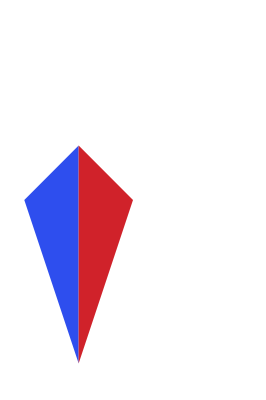
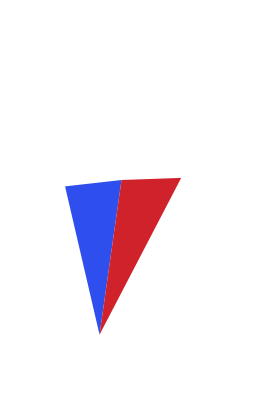
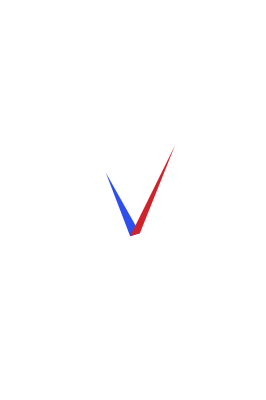
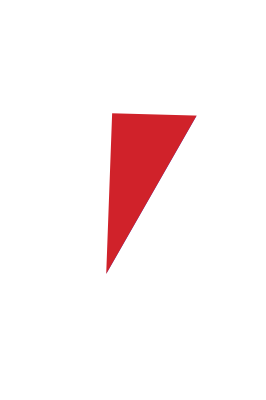
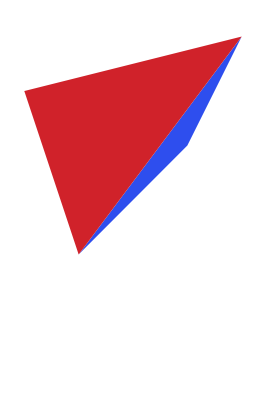
{0.237467,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[ListAnimation[5,LocalAlexa,QuadraticFormAlexa,ConstPair[1],Configuration2]]
```

```mathematica
dataS2={{-1.0,1.0}, {0.0,-2.0},{1.0,1.0},{0.0,2.0}};
dataE2={{2.0,2.0},{3.0,4.0},{-1.0,3.0},{0.0,0.0}};
dataT2={{1,2,4}, {2,3,4}};
Configuration2={dataS2,dataE2,dataT2};Timing[ListAnimationc[5,Configuration2]]
```

{0.014257,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

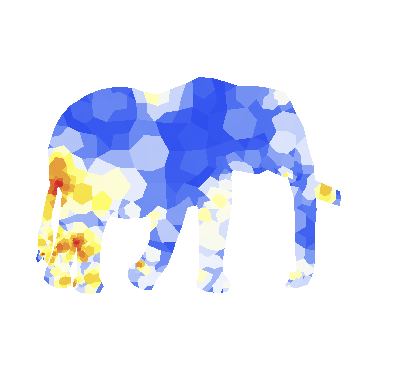
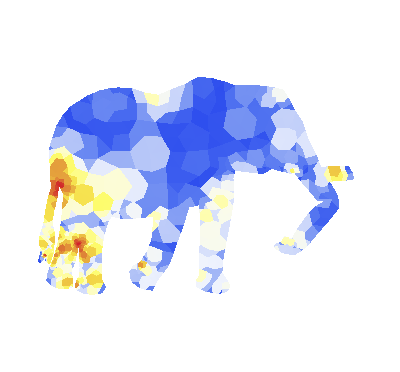
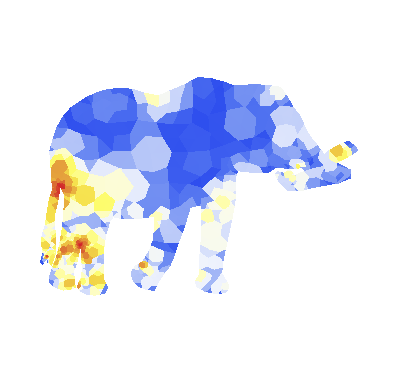
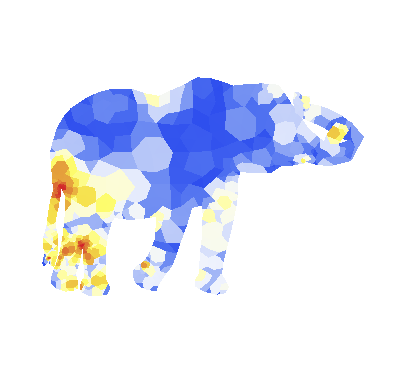
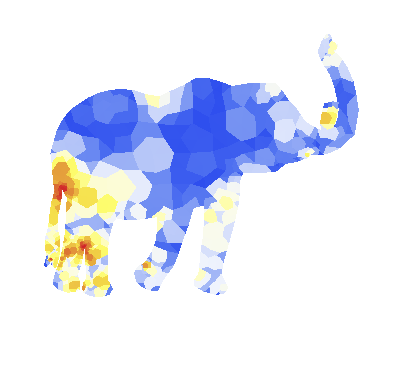

```mathematica
Off[General::luc];
ListAnimationc[5,ConfigurationElephant]
```

```mathematica
DrawAnimation[LocalAlexa,QuadraticFormAlexa,ConstPair[1],Configuration2]
```

```mathematica
DrawAnimationc[5,Configuration2]
```

```mathematica
DrawAnimationc[5,ConfigurationElephant]
```

Inverse::luc: 行列{{55171.6,0.,-23117.6,0.,0.,0.,0.,0.,-11480.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-15124.6,0.,0.,0.,0.,0.,-5447.96,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«2160»},«49»,«2160»}に含まれる悪条件より，Inverseの結果には重大な数値誤差が含まれている可能性があります．

General::stop: この計算中に，Inverse::lucのこれ以上の出力は表示されません．